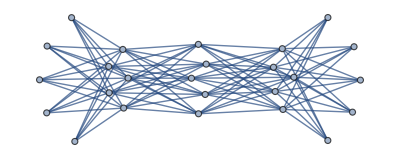

```mathematica
bertha25 = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/Bertha_25.graphml"]
```

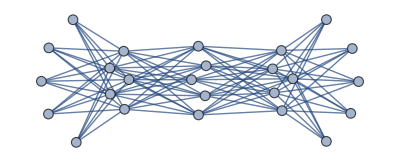

```mathematica
Graph[bertha25,VertexSize->.5]
```

```mathematica
Eigenvectors[N[Normal[AdjacencyMatrix[bertha25]]]]
```

{{0.129099,0.129099,0.129099,0.129099,0.129099,0.223607,0.223607,0.223607,0.223607,0.223607,0.258199,0.258199,0.258199,0.258199,0.258199,0.223607,0.223607,0.223607,0.223607,0.223607,0.129099,0.129099,0.129099,0.129099,0.129099},{0.129099,0.129099,0.129099,0.129099,0.129099,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,0.258199,0.258199,0.258199,0.258199,0.258199,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,0.129099,0.129099,0.129099,0.129099,0.129099},{0.223607,0.223607,0.223607,0.223607,0.223607,0.223607,0.223607,0.223607,0.223607,0.223607,5.55112×10^-17,5.55112×10^-17,5.55112×10^-17,5.55112×10^-17,5.55112×10^-17,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607},{-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,0.223607,0.223607,0.223607,0.223607,0.223607,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-0.223607,-0.223607,-0.223607,-0.223607,-0.223607,0.223607,0.223607,0.223607,0.223607,0.223607},{0.0716115,0.0716115,0.0716115,0.0716115,0.0716115,5.0307×10^-17,5.0307×10^-17,5.0307×10^-17,5.0307×10^-17,5.0307×10^-17,-0.0716115,-0.0716115,-0.0716115,-0.0716115,-0.0716115,0.,0.,0.,0.,0.,-0.143223,-0.143223,-0.143223,-0.143223,0.930949},{0.0841626,0.0841626,0.0841626,0.0841626,0.0841626,5.55112×10^-17,5.55112×10^-17,5.55112×10^-17,5.55112×10^-17,5.55112×10^-17,-0.0841626,-0.0841626,-0.0841626,-0.0841626,-0.0841626,-3.46945×10^-17,-3.46945×10^-17,-3.46945×10^-17,-3.46945×10^-17,1.04083×10^-16,0.0656072,0.795017,-0.53303,0.0932192,0.},{0.0604481,0.0604481,0.0604481,0.0604481,0.0604481,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-0.0604481,-0.0604481,-0.0604481,-0.0604481,-0.0604481,5.55112×10^-17,-5.55112×10^-17,-5.55112×10^-17,-1.66533×10^-16,1.66533×10^-16,0.5215,-0.433746,-0.382838,0.597325,0.},{-0.0180961,-0.0180961,-0.0180961,-0.0180961,-0.127824,2.22045×10^-17,2.22045×10^-17,2.22045×10^-17,-3.33067×10^-17,-3.33067×10^-17,0.208953,0.0489988,-0.019248,-0.019248,-0.019248,-0.297133,-0.0379799,-0.0379799,-0.418814,0.791907,-0.149665,-0.0267473,-0.106989,0.0831937,0.},{-0.0120384,-0.0120384,-0.0120384,-0.0120384,-0.158718,-4.93038×10^-32,-4.93038×10^-32,-4.93038×10^-32,-4.93038×10^-32,-4.93038×10^-32,0.14894,0.087823,-0.00996364,-0.00996364,-0.00996364,-0.0504802,0.108423,0.108423,0.0788314,-0.245197,-0.703112,-0.019239,-0.0769562,0.592436,0.},{0.140926,0.140926,0.140926,0.140926,0.244586,2.77556×10^-18,2.80331×10^-16,2.77556×10^-18,7.21645×10^-17,-3.58047×10^-16,-0.162994,-0.411276,-0.0780063,-0.0780063,-0.0780063,0.109745,-0.292612,-0.292612,0.216674,0.258806,-0.101034,0.118785,0.47514,0.315397,0.},{-0.0123155,-0.0123155,-0.0123155,-0.0123155,0.210373,5.27356×10^-17,6.35603×10^-16,5.27356×10^-17,-3.05311×10^-17,-7.10543×10^-16,0.415038,-0.60557,0.009807,0.009807,0.009807,-0.465209,0.284516,0.284516,0.031134,-0.134956,0.0922369,0.0219559,0.0878237,-0.0409053,0.},{0.267881,0.267881,0.267881,0.267881,-0.726507,1.76248×10^-16,-9.75608×10^-16,1.76248×10^-16,-2.40086×10^-16,8.63198×10^-16,0.0382561,-0.157172,-0.0753675,-0.0753675,-0.0753675,0.0931642,0.107868,0.107868,-0.203441,-0.105459,0.132402,0.0480156,0.192062,-0.0274615,0.},{0.0221976,0.0221976,0.0221976,0.0221976,-0.351726,1.11022×10^-17,-1.83187×10^-16,1.11022×10^-17,-1.66533×10^-17,1.77636×10^-16,0.127067,0.102585,0.0110947,0.0110947,0.0110947,-0.426332,-0.205003,-0.205003,0.726582,0.109756,0.0477544,-0.0388687,-0.155475,-0.116347,0.},{-0.0823103,-0.0823103,-0.0823103,-0.0823103,-0.227383,2.01228×10^-16,-1.09635×10^-15,2.01228×10^-16,-2.35922×10^-16,9.29812×10^-16,0.0386345,-0.518184,0.345391,0.345391,0.345391,0.334089,-0.171038,-0.171038,-0.0278107,0.035798,-0.111754,-0.0790242,-0.316097,-0.0497493,0.},{0.0359013,0.0359013,0.0359013,0.0359013,-0.0443173,2.55351×10^-16,1.26843×10^-15,2.55351×10^-16,-3.69149×10^-16,-1.40998×10^-15,-0.753015,-0.0329064,0.228878,0.228878,0.228878,-0.422666,0.193171,0.193171,-0.0195201,0.0558438,-0.0458841,0.0151038,0.0604151,0.069653,0.},{0.104949,-0.109613,-0.109613,0.114278,-6.11561×10^-16,0.289193,-0.135268,0.289193,-0.317179,-0.125939,2.4347×10^-16,-3.42866×10^-16,0.167252,-0.375245,0.207994,4.04879×10^-16,-0.467882,0.467882,1.96712×10^-16,-7.39743×10^-17,-2.95846×10^-17,7.40149×10^-17,7.40149×10^-17,8.32667×10^-17,0.},{-0.151443,0.158188,0.160307,-0.167052,-3.09028×10^-15,-0.208044,0.123903,-0.208044,0.0644799,0.227705,1.72056×10^-15,-2.52431×10^-15,-0.117128,0.380923,-0.263795,2.66948×10^-15,-0.506016,0.506016,-2.58734×10^-16,-3.59299×10^-16,-2.88847×10^-17,-1.68846×10^-16,-5.64363×10^-16,-3.88578×10^-16,0.},{0.191907,-0.202879,-0.196495,0.207468,1.67452×10^-16,-0.343704,0.0509176,-0.343704,0.620251,0.0162397,-6.72971×10^-16,7.3394×10^-17,0.081143,-0.332286,0.251143,-7.03631×10^-16,-0.135007,0.135007,1.0128×10^-16,4.92179×10^-17,-4.06655×10^-17,5.55112×10^-17,2.22045×10^-16,1.52656×10^-16,0.},{-0.10429,0.12895,0.0729123,-0.0975725,-1.47696×10^-15,0.174576,-0.0804806,0.174576,0.380678,-0.649349,1.01194×10^-15,-7.73959×10^-16,-0.455213,0.20351,0.251703,1.46997×10^-15,-0.076384,0.076384,-2.12715×10^-16,-1.57148×10^-16,4.44849×10^-17,-1.31839×10^-16,-5.27356×10^-16,-2.56739×10^-16,0.},{-0.212683,-0.109309,0.176498,0.145494,-4.42068×10^-16,0.0974674,-0.176922,0.0974674,0.316683,-0.334696,2.32837×10^-16,1.87083×10^-16,0.559136,0.00188184,-0.561018,3.15645×10^-16,-0.0159496,0.0159496,-8.59432×10^-17,-8.76675×10^-17,3.64817×10^-17,-6.55581×10^-17,-2.06721×10^-16,-1.68268×10^-16,0.},{0.340549,-0.533711,-0.25039,0.443552,-8.9896×10^-16,0.0505727,0.0772278,0.0505727,-0.100501,-0.0778718,1.77328×10^-15,-1.5627×10^-15,-0.226657,0.455507,-0.22885,1.47648×10^-15,-0.0251886,0.0251886,-2.14004×10^-16,-5.17325×10^-17,7.21325×10^-17,0.,0.,-4.68375×10^-17,0.},{0.538968,0.204933,-0.287718,-0.456184,-8.54642×10^-16,-0.0241009,0.419749,-0.0241009,-0.0418624,-0.329684,7.02746×10^-16,-3.7683×10^-17,0.213886,-0.00670255,-0.207183,9.32596×10^-16,-0.00771367,0.00771367,-8.22173×10^-17,-2.03641×10^-16,5.35618×10^-17,5.78241×10^-19,-3.30754×10^-16,-1.81712×10^-16,0.},{0.439484,-0.0647146,0.00333415,-0.378104,9.12983×10^-16,0.101743,-0.703601,0.101743,0.222227,0.277888,-5.69503×10^-16,-2.17442×10^-16,-0.0360881,0.105692,-0.069604,-7.98203×10^-16,-0.00212886,0.00212886,-1.79027×10^-17,5.15141×10^-17,-1.49003×10^-17,8.55797×10^-17,4.53341×10^-16,2.11311×10^-16,0.},{0.153313,-0.558741,0.701228,-0.2958,-1.59679×10^-16,-0.0385441,0.220844,-0.0385441,-0.0639267,-0.0798289,-1.13457×10^-16,2.59292×10^-16,-0.0107472,-0.101088,0.111835,7.78171×10^-18,0.00451848,-0.00451848,-4.33926×10^-17,5.1657×10^-18,2.29872×10^-16,-5.43547×10^-17,-1.06396×10^-16,-1.83447×10^-16,0.},{5.99882×10^-16,-9.45391×10^-15,9.26759×10^-15,-4.15554×10^-16,4.21787×10^-18,0.707107,1.95558×10^-16,-0.707107,-1.89431×10^-16,-1.7559×10^-17,2.10826×10^-18,-3.46813×10^-18,-5.06564×10^-17,1.73776×10^-16,-1.26221×10^-16,4.64886×10^-18,1.25837×10^-18,5.42287×10^-18,6.90307×10^-18,-1.82332×10^-17,7.54893×10^-18,-8.83916×10^-18,1.5769×10^-17,-1.00174×10^-17,0.}}

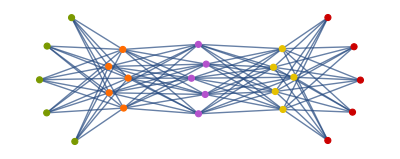

```mathematica
HighlightGraph[AdjacencyGraph[Normal[AdjacencyMatrix[bertha25]]],{{1,2,3,4,5},{6,7,8,9,10},{11,12,13,14,15},{16,17,18,19,20},{21,22,23,24,25}}]
```

```mathematica
Graph[bertha25]
```

-Graphics-

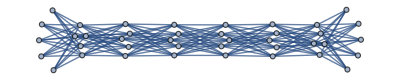

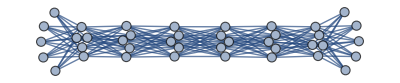

```mathematica
bertha40 = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/Bertha_40.graphml"]
bertha40=Graph[bertha40,VertexSize->1.0,VertexStyle->{1->Red}]
```

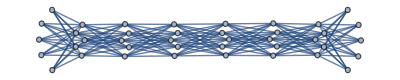

```mathematica
bertha40_new = Graph[EdgeList[bertha40]]
```

```mathematica
{{1,2,3,4,5},{6,7,8,9,10},{11,12,13,14,15},{16,17,18,19,20},{21,22,23,24,25}, {26,27,28,29,30}, {31,32,33,34,35}, {36,37,38,39,40}}
```

```mathematica
HighlightGraph[AdjacencyGraph[Normal[AdjacencyMatrix[bertha40]]],VertexStyle->{{1->Red}]
```

-Graphics-

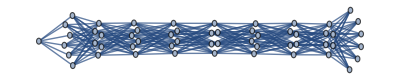

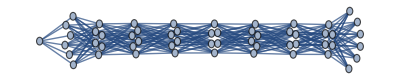

```mathematica
bertha55 = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/Bertha_55.graphml"]
Graph[bertha55,VertexSize->1]
```

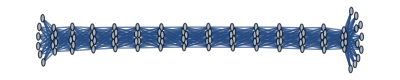

```mathematica
bertha100 = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/Bertha_100.graphml"]
```

```mathematica
Eigenvectors[AdjacencyMatrix[bertha100]]
```

$Aborted

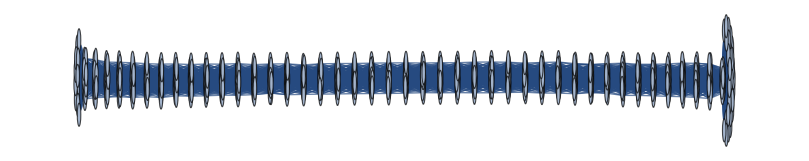

```mathematica
bertha500 = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/Bertha_500.graphml"]
```

```mathematica
bertha1000 = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/Bertha_1000.graphml"]
```

```mathematica
Graph[bertha1000]
```